# Risposta alla rampa per un sistema LTI-TD

```mathematica
Clear["Global`*"]
```

```mathematica
A={{11/12,-1,31/12},{1,-1,1},{1/12,0,-7/12}};B={{1},{0},{-1}};C1={{-1,3/2,-1}};
```

```mathematica
G[z_]:=Simplify[(C1.Inverse[z IdentityMatrix[3]-A].B)[[1]][[1]]]
```

```mathematica
G[z]
```

(6 (-1+2 z))/((1+2 z)^2 (-1+3 z))

```mathematica
yrampaz=G[z](z/(z-1)^2)
```

(6 z (-1+2 z))/((-1+z)^2 (1+2 z)^2 (-1+3 z))

```mathematica
Subscript[C, 11](1/(z-1))+Subscript[C, 12](1/(z-1)^2)+Subscript[C, 21](1/(z+1/2))+Subscript[C, 22](1/(z+1/2)^2)+Subscript[C, 3](1/(z-1/3))
```

C_3/(-1/3+z)+C_11/(-1+z)+C_12/(-1+z)^2+C_21/(1/2+z)+C_22/(1/2+z)^2

```mathematica
Subscript[C, 3]=lim_(z->1/3) (z-1/3)(yrampaz/z)
```

-27/50

```mathematica
Subscript[C, 12]=lim_(z->1) (z-1)^2(yrampaz/z)
```

1/3

```mathematica
Subscript[C, 11]=lim_(z->1) D[(z-1)^2(yrampaz/z),z]
```

-5/18

```mathematica
Subscript[C, 22]=lim_(z->-1/2) (z+1/2)^2(yrampaz/z)
```

8/15

```mathematica
Subscript[C, 21]=lim_(z->-1/2) D[(z+1/2)^2(yrampaz/z),z]
```

184/225

```mathematica
Subscript[C, 11](z/(z-1))+Subscript[C, 12](z/(z-1)^2)+Subscript[C, 21](z/(z+1/2))+Subscript[C, 22](z/(z+1/2)^2)+Subscript[C, 3](z/(z-1/3))
```

```mathematica
Subscript[y, -2][k_]:=Subscript[C, 11] UnitStep[k]+Subscript[C, 12] k UnitStep[k]+Subscript[C, 21](-1/2)^k UnitStep[k]+Subscript[C, 22] Binomial[k,1](-1/2)^(k-1)UnitStep[k]+Subscript[C, 3](1/3)^k UnitStep[k]
```

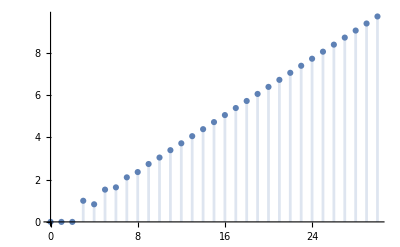

```mathematica
DiscretePlot[Subscript[y, -2][k],{k,0,30},PlotRange->All]
```

```mathematica
Subscript[y, ss][k_]:=Subscript[C, 11] UnitStep[k]+Subscript[C, 12] k UnitStep[k]
```

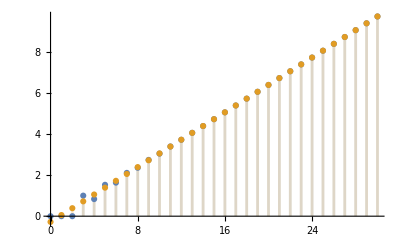

```mathematica
DiscretePlot[{Subscript[y, -2][k],Subscript[y, ss][k]},{k,0,30},PlotRange->All]
```